# Auto-grader for Open Ended Math Problems

### Determining Equivalent Responses and Classifying Problems for Proper Evaluation of student response

Silas Kurt Grossberndt
Robert Nachbar

#### Abstract

In order to automatically grade student problems one must identify the scope and level of the problem and then define equivalent answers appropriate to the context of the question and knowledge of the student. To this end, we first train a Neural Network Classifier on a data set of problems in Algebra 1, Algebra 2 and Calculus. Then, using a combination of rule based checks and the theorem prover, we define equivalent answers, then check that particular rules were not used in order to maintain equivalence at the level of the student to prevent cheating. All of this is then packaged in a GUI for understandability.

## Introduction

When providing questions to students online, the teacher is often left with a dilemma. Do  you give the student a multiple choice problem that fails to properly test their ability by allowing guessing, or do you give them a long answer that will only accept one correct answer, when there might be multiple equivalent answers? To add in all possible answers would be an onerous task, thus it would be preferable to have the system automatically identify all possible answers. However, this presents a challenge in its own right. How does one limit the possible answers to those that the student would have reached based on the level of their knowledge, and how does one deal with problems that may limit the scope of the equivalent answers? To this end, we define a two part problem: classification of the problem’s level and scope and cross checking for equivalent answers.

## Classifying and Identifying Problems

### Classifying Questions to determine the level of the problem

The problem of classification is often solved by machine learning techniques trained on large data sets. In this case, I retrained a series of models in the Wolfram language “Classify” function on a 1800 question data set in algebra 1, 2  and calculus, grouping all the problems and providing the problems and groupings to the network, i.e. training in a supervised manner. Then, the accuracy of each model was tested by comparing the probability of identification as the proper grouping to the highest probability of the other two groups, using:

```mathematica
Clear[questionClassifier]
questionClassifier=Classify[<|"algebra 1"->algebra1Questions, "algebra 2"->algebra2Qs,"calc"->calcQs|> , PerformanceGoal->"Quality"]

calcIsCalc=questionClassifier[calcQs, {"Probability", "calc"}];
calcIsAlgebra1=questionClassifier[calcQs, {"Probability", "algebra 1"}];
calcIsAlgebra2=questionClassifier[calcQs, {"Probability", "algebra 2"}];
algebra1IsCalc=questionClassifier[algebra1Questions, {"Probability", "calc"}];
algebra1IsAlgebra1=questionClassifier[algebra1Questions, {"Probability", "algebra 1"}];
algebra1IsAlgebra2=questionClassifier[algebra1Questions, {"Probability", "algebra 2"}];
algebra2IsCalc=questionClassifier[algebra2Qs, {"Probability", "calc"}];
algebra2IsAlgebra1=questionClassifier[algebra2Qs, {"Probability", "algebra 1"}];
algebra2IsAlgebra2=questionClassifier[algebra2Qs, {"Probability", "algebra 2"}];
ListLogPlot[calcIsCalc⟦#⟧/Max[calcIsAlgebra1⟦#⟧,calcIsAlgebra2⟦#⟧]
&/Range[600],AxesLabel->{"Training Set","Ratio of Probaility"}, 
PlotLabel-> "Correct Identification as Calculus"]
ListLogPlot[algebra1IsAlgebra1⟦#⟧/Max[algebra1IsCalc⟦#⟧,algebra1IsAlgebra2⟦#⟧]
&/Range[600],AxesLabel->{"Training Set","Ratio of Probaility"}, 
PlotLabel-> "Correct Identification as Algebra 1"]
ListLogPlot[algebra2IsAlgebra2⟦#⟧/Max[algebra2IsAlgebra1⟦#⟧,algebra2IsCalc⟦#⟧]
&/Range[600],AxesLabel->{"Training Set","Ratio of Probaility"}, 
PlotLabel-> "Correct Identification as Algebra 2"]
```

All models were given the “Quality” goal to improve accuracy at the cost of training time, as the training is taking place ahead of time, and the system is not retrained live. However, when this was performed on data generated by the Wolfram|Alpha Problem Generator, where the addition of calculus made “What is 1+1” evaluate as calculus independent of the number of inputs. Total training inputs are 1500, with 750 each of algebra 1 and 2.

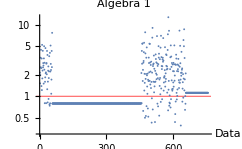
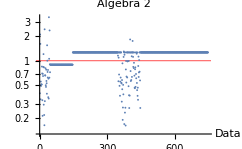
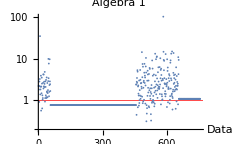
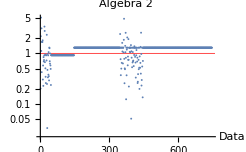
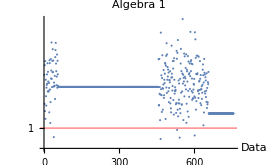
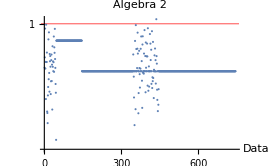
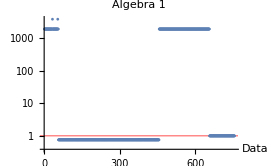
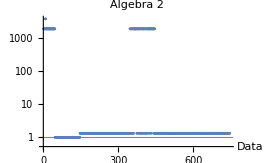
Method | Algebra1  | Algebra 2 | Accuracy
Automatic | -Graphics- | -Graphics- | 0.58
Neural Network | -Graphics- | -Graphics- | 0.59
Logistic Regression | -Graphics- | -Graphics- | 0.50
Naive Bayesian | -Graphics- | -Graphics- | 0.67
Nearest Neighbor | -Graphics- | -Graphics- | 0.57
Gradiant Boosted Trees | -Graphics- | -Graphics- | 0.59
Markov | -Graphics- | -Graphics- | 0.93
Support Vector Machine | -Graphics- | -Graphics- | 0.57
Random Forest | -Graphics- | -Graphics- | 0.63
Decision Tree | -Graphics- | -Graphics- | 0.50

It is thus obvious to select the Markov model for the classifier.

### Identifying the Context of the Problem

The context of the problem, however, does not get captured by the classifier above. The classifier simply finds the level, meanwhile the context, for example, would be “write your answer as a simplified fraction”. These contexts are identified via pattern matching. These rules are then used to assign a specific tag:

Value | Meaning
0 | No Context Restrictions
1 | Simplest Form Fraction
2 | Decimal Representation
3 | A set of Points
4 | Calculus
5 | A set of Points of Simplest Fractions
6 | A set of Points in Decimal
7 | Mixed Number
8 | Improper Fraction

The rules were given by :

```mathematica
turnOffEquivFrac[question_]:=StringMatchQ[question, {"*raction*implest form"}];
isMatrix[answer_]:=MatchQ[answer, MatrixForm];
allpoints[question_]:=StringMatchQ[question, {"*all points*"}];
eitherPointfirst[a_, b_,c_, d_]:= {{"(",a, b, ")"},{"("c, d ")"}}-> {{"("c, d ")"},{"(",a, b, ")"}}
isPoint[answer_]:=StringMatchQ[answer, {"(*,*)"}];
improperFraction[question_]:=StringMatchQ[question, "*mproper fraction*"];
decForm[question_]:=StringMatchQ[question, "*ecimal form*"];
isCalc[question_]:=StringMatchQ[question, {"*erivative*", "*ifferniate*", "*ntegra*", "*aylor*xpand*", "*acLa*xpand*", "*imit*"}];
mixedNumber[question_]:=StringMatchQ[question, "*ixed number*"];
```

Note that the calculus rule here will serve as the classifier for calculus, which is likely to leave a gap of problems given symbolically. One method to deal with this is discussed in the conclusion.

## Identifying Equivalent Responses

In order to provide a more robust and deployable version of the autograder, the identification of context and equivalent responses are handled in a new package, “Math Autograder”.

### Rule Based Identification

In order to perform checks on the context restricted identification, one performs the following for tags 1,2,7 and 8:

```mathematica
1|2|7|8, If[correctAnswer[answer, correct], True, False],
```

And for tags 5 and 6, one does the following to check if the data are equivalent except for ordering of the points:

```mathematica
5|6, If[Complement[StringSplit[answer, "),("], StringSplit[correct, "),("]]=={}, True, False
```

### Theorem Prover Based Identification

In the majority of cases, the first test is still rule based:

In order to reject answers that would give false positive, or answers that would be beyond the level of the student, we also implement the theorem prover:

## Conclusion

This project has developed a Classifier and a Package that may be implemented in a variety of applications. Below are two exemplars. One has the student submits an answer to a randomly selected question from a database that has been built using Wolfram|Alpha’s Problem Generator. The student may select one of the three levels, receive a question, submit an answer and check that it is correct. After the correct answer has been submitted, the system automatically pulls a new question from the list in the selected type. The second allows for the teacher to create a quiz and store it as a new database, which will then be fed to the first exemplar. Thus, we see this project as a quiet sever side application, and as a service that would be deliverable to a client. Further work could encompass the addition of further levels of question, the use of graphical data as a selected answer or the inclusion of a retraining function in the neural net to improve classification accuracy.

## Exemplar Implementation

```mathematica
studentModule=DynamicModule[{question, type, answer, correctanswer, f},
pnumber=RandomInteger[{0,Length[algebra2Qsq]}];
FormFunction[{
			"Type of Problem"-> Restricted["String", {"Algebra 1", "Algebra 2 and Trig", "Calculus"}]-> "Algebra 1", 
			#level&, 
			problems[TemplateSlot["level"]]⟦1⟧⟦RandomInteger[{0, 120}]⟧ ,
			"Answer"-> "String"},
			  AppearanceRules-> <|"Title"-> "Student Problem Generator", "Description"->"Randomly Generated problems in selected topic", "SubmitLabel"-> "Check Answer", "BackgroundColor"->LightBlue|>,
			f];
(*package here*)
]
CloudDeploy[studentModule]
```

## Initialization Cells